```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
n=30;
```

```mathematica
Pts=Table[N[1/2{Cos[(2π)/n(i-1)],Sin[(2π)/n(i-1)]}],{i,1,n}];
```

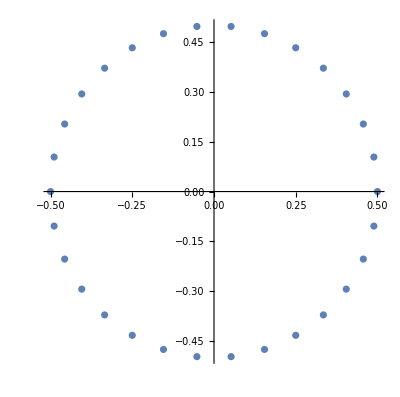

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
Export["Circle"<>ToString[n],{"#This is a textfile with points on circular airfoil with radius 1"}~Join~{"np = "<>ToString[n]}~Join~{"r = { \\"}~Join~((ToString[#]<>", \\")&/@(Pts[[1;;-2]]))~Join~((ToString[#]<>" \\")&/@(Pts[[{-1}]]))~Join~{" }"}]
```

Circle30.txt